```mathematica
$Assumptions=ϕA∈Reals &&ϕB∈Reals && ϕAB∈Reals && AA∈PositiveReals && BB∈PositiveReals
```

ϕA∈ℝ&&ϕB∈ℝ&&ϕAB∈ℝ&&AA∈ℝ&&AA>0&&BB∈ℝ&&BB>0

```mathematica
rho12 = Exp[I(ϕB+ϕAB)]Exp[-BB]
rho13 = Exp[I (-ϕA + ϕAB)]Exp[-AA]
rho14 = Exp[I (-ϕA + ϕB)]Exp[-AA+BB]
rho23 = Exp[I (-ϕA-ϕB)]Exp[-AA-BB]
rho24 = Exp[I (-ϕA-ϕAB)]Exp[-AA]
rho34 = Exp[I (ϕB-ϕAB)]Exp[-BB]
rho = Simplify[(1/4)*{{ 1, Conjugate[rho12] , rho13, rho23}, {rho12, 1, rho14, rho24}, {Conjugate[rho13], Conjugate[rho14], 1, Conjugate[rho34]}, {Conjugate[rho23], Conjugate[rho24], rho34, 1}}]
```

ⅇ^(-BB+ⅈ (ϕAB+ϕB))

ⅇ^(-AA+ⅈ (-ϕA+ϕAB))

ⅇ^(-AA+BB+ⅈ (-ϕA+ϕB))

ⅇ^(-AA-BB+ⅈ (-ϕA-ϕB))

ⅇ^(-AA+ⅈ (-ϕA-ϕAB))

ⅇ^(-BB+ⅈ (-ϕAB+ϕB))

{{1/4,1/4 ⅇ^(-BB-ⅈ (ϕAB+ϕB)),1/4 ⅇ^(-AA+ⅈ (-ϕA+ϕAB)),1/4 ⅇ^(-AA-BB-ⅈ (ϕA+ϕB))},{1/4 ⅇ^(-BB+ⅈ (ϕAB+ϕB)),1/4,1/4 ⅇ^(-AA+BB+ⅈ (-ϕA+ϕB)),1/4 ⅇ^(-AA-ⅈ (ϕA+ϕAB))},{1/4 ⅇ^(-AA+ⅈ (ϕA-ϕAB)),1/4 ⅇ^(-AA+BB+ⅈ (ϕA-ϕB)),1/4,1/4 ⅇ^(-BB+ⅈ (ϕAB-ϕB))},{1/4 ⅇ^(-AA-BB+ⅈ (ϕA+ϕB)),1/4 ⅇ^(-AA+ⅈ (ϕA+ϕAB)),1/4 ⅇ^(-BB+ⅈ (-ϕAB+ϕB)),1/4}}

```mathematica
MatrixForm[rho]
```

(1/4 | 1/4 ⅇ^(-BB-ⅈ (ϕAB+ϕB)) | 1/4 ⅇ^(-AA+ⅈ (-ϕA+ϕAB)) | 1/4 ⅇ^(-AA-BB-ⅈ (ϕA+ϕB))
1/4 ⅇ^(-BB+ⅈ (ϕAB+ϕB)) | 1/4 | 1/4 ⅇ^(-AA+BB+ⅈ (-ϕA+ϕB)) | 1/4 ⅇ^(-AA-ⅈ (ϕA+ϕAB))
1/4 ⅇ^(-AA+ⅈ (ϕA-ϕAB)) | 1/4 ⅇ^(-AA+BB+ⅈ (ϕA-ϕB)) | 1/4 | 1/4 ⅇ^(-BB+ⅈ (ϕAB-ϕB))
1/4 ⅇ^(-AA-BB+ⅈ (ϕA+ϕB)) | 1/4 ⅇ^(-AA+ⅈ (ϕA+ϕAB)) | 1/4 ⅇ^(-BB+ⅈ (-ϕAB+ϕB)) | 1/4)

```mathematica
FullSimplify[Eigenvalues[rho]]
```

{1/8 ⅇ^(-AA-BB-ⅈ ϕAB) (-ⅇ^(ⅈ ϕAB) (1+ⅇ^(2 BB)-2 ⅇ^(AA+BB))-√(-4 ⅇ^(AA+BB)-4 ⅇ^(AA+BB+4 ⅈ ϕAB)+ⅇ^(2 ⅈ ϕAB) (1+4 ⅇ^(2 AA)+2 ⅇ^(2 BB)+ⅇ^(4 BB)))),1/8 ⅇ^(-AA-BB-ⅈ ϕAB) (-ⅇ^(ⅈ ϕAB) (1+ⅇ^(2 BB)-2 ⅇ^(AA+BB))+√(-4 ⅇ^(AA+BB)-4 ⅇ^(AA+BB+4 ⅈ ϕAB)+ⅇ^(2 ⅈ ϕAB) (1+4 ⅇ^(2 AA)+2 ⅇ^(2 BB)+ⅇ^(4 BB)))),1/8 ⅇ^(-AA-BB-ⅈ ϕAB) (ⅇ^(ⅈ ϕAB) (1+ⅇ^(2 BB)+2 ⅇ^(AA+BB))-√(4 ⅇ^(AA+BB)+4 ⅇ^(AA+BB+4 ⅈ ϕAB)+ⅇ^(2 ⅈ ϕAB) (1+4 ⅇ^(2 AA)+2 ⅇ^(2 BB)+ⅇ^(4 BB)))),1/8 ⅇ^(-AA-BB-ⅈ ϕAB) (ⅇ^(ⅈ ϕAB) (1+ⅇ^(2 BB)+2 ⅇ^(AA+BB))+√(4 ⅇ^(AA+BB)+4 ⅇ^(AA+BB+4 ⅈ ϕAB)+ⅇ^(2 ⅈ ϕAB) (1+4 ⅇ^(2 AA)+2 ⅇ^(2 BB)+ⅇ^(4 BB))))}

```mathematica
rhorho = FullSimplify[rho.ConjugateTranspose[rho]]
```

{{1/4 ⅇ^(-AA-BB) Cosh[AA] Cosh[BB],1/16 ⅇ^(-2 AA-BB-ⅈ (ϕAB+ϕB)) (2 ⅇ^(2 AA)+ⅇ^(2 ⅈ ϕAB) (1+ⅇ^(2 BB))),1/16 ⅇ^(-AA-2 BB-ⅈ (ϕA+ϕAB)) (1+ⅇ^(2 BB) (1+2 ⅇ^(2 ⅈ ϕAB))),1/16 ⅇ^(-AA-BB-ⅈ (ϕA+2 ϕAB+ϕB)) (1+ⅇ^(2 ⅈ ϕAB))^2},{1/16 ⅇ^(-2 AA-BB-ⅈ ϕAB+ⅈ ϕB) (1+ⅇ^(2 BB)+2 ⅇ^(2 AA+2 ⅈ ϕAB)),1/4 ⅇ^-AA Cosh[AA-BB] Cosh[BB],1/16 ⅇ^(-AA-BB-ⅈ (ϕA+2 ϕAB-ϕB)) (1+2 ⅇ^(2 BB+2 ⅈ ϕAB)+ⅇ^(4 ⅈ ϕAB)),1/16 ⅇ^(-AA-2 BB-ⅈ (ϕA+ϕAB)) (2 ⅇ^(2 BB)+ⅇ^(2 ⅈ ϕAB) (1+ⅇ^(2 BB)))},{1/8 ⅇ^(-AA-BB+ⅈ ϕA) (2 Cos[ϕAB] Cosh[BB]+ⅇ^(-ⅈ ϕAB) Sinh[BB]),1/16 ⅇ^(-AA-BB+ⅈ (ϕA-2 ϕAB-ϕB)) (1+2 ⅇ^(2 BB+2 ⅈ ϕAB)+ⅇ^(4 ⅈ ϕAB)),1/4 ⅇ^-AA Cosh[AA-BB] Cosh[BB],1/16 ⅇ^(-2 AA-BB-ⅈ (ϕAB+ϕB)) (1+ⅇ^(2 BB)+2 ⅇ^(2 AA+2 ⅈ ϕAB))},{1/16 ⅇ^(-AA-BB+ⅈ (ϕA-2 ϕAB+ϕB)) (1+ⅇ^(2 ⅈ ϕAB))^2,1/16 ⅇ^(-AA-2 BB+ⅈ (ϕA-ϕAB)) (1+ⅇ^(2 BB) (1+2 ⅇ^(2 ⅈ ϕAB))),1/16 ⅇ^(-2 AA-BB-ⅈ ϕAB+ⅈ ϕB) (2 ⅇ^(2 AA)+ⅇ^(2 ⅈ ϕAB) (1+ⅇ^(2 BB))),1/4 ⅇ^(-AA-BB) Cosh[AA] Cosh[BB]}}

```mathematica
eigenvalsrhorho = FullSimplify[Eigenvalues[rhorho]]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

{0,1,0,0}

```mathematica
FullSimplify[Total[Sqrt[eigenvalsrhorho]]]
```

1+Abs[Sin[ϕAB]]

```mathematica
rhoTest = 1/4 {{1, Exp[-I x], Exp[I x], 1}, {Exp[I x], 1, 1, Exp[-I x]}, {Exp[-I x], 1, 1, Exp[I x]}, {1, Exp[I x], Exp[-I x], 1}}
```

{{1/4,ⅇ^(-ⅈ x)/4,ⅇ^(ⅈ x)/4,1/4},{ⅇ^(ⅈ x)/4,1/4,1/4,ⅇ^(-ⅈ x)/4},{ⅇ^(-ⅈ x)/4,1/4,1/4,ⅇ^(ⅈ x)/4},{1/4,ⅇ^(ⅈ x)/4,ⅇ^(-ⅈ x)/4,1/4}}

```mathematica
eig = FullSimplify[Eigenvalues[rhoTest]]
```

{Sin[x/2]^2,Cos[x/2]^2,Sin[x]/2,-Sin[x]/2}

```mathematica
$Assumptions = x∈Reals
FullSimplify[Total[Abs[eig]]]
```

x∈ℝ

Total[Abs[eig]]

```mathematica
1+Abs[Sin[x]]
```

```mathematica
W = KroneckerProduct[IdentityMatrix[2], IdentityMatrix[2]] + KroneckerProduct[PauliMatrix[1], PauliMatrix[3]] + KroneckerProduct[PauliMatrix[2], PauliMatrix[2]];
MatrixForm[W]
```

(1 | 0 | 1 | -1
0 | 1 | 1 | -1
1 | 1 | 1 | 0
-1 | -1 | 0 | 1)

```mathematica
$Assumptions ϕ1∈ Reals && ϕ2∈ Reals;
rho = 1/4*{{1 ,Exp[-I ϕ1], Exp[-I ϕ2], 1}, { Exp[I ϕ1], 1, Exp[I(ϕ1 - ϕ2)], Exp[I ϕ1]},  {Exp[I ϕ2], Exp[I(ϕ2 - ϕ1)], 1, Exp[I ϕ2]}, {1, Exp[-I ϕ1], Exp[-I ϕ2], 1}};
MatrixForm[rho]
```

(1/4 | ⅇ^(-ⅈ ϕ1)/4 | ⅇ^(-ⅈ ϕ2)/4 | 1/4
ⅇ^(ⅈ ϕ1)/4 | 1/4 | 1/4 ⅇ^(ⅈ (ϕ1-ϕ2)) | ⅇ^(ⅈ ϕ1)/4
ⅇ^(ⅈ ϕ2)/4 | 1/4 ⅇ^(ⅈ (-ϕ1+ϕ2)) | 1/4 | ⅇ^(ⅈ ϕ2)/4
1/4 | ⅇ^(-ⅈ ϕ1)/4 | ⅇ^(-ⅈ ϕ2)/4 | 1/4)

```mathematica
w1 = FullSimplify[Tr[W.rho]]
```

1/2 (1-Cos[ϕ1]+Cos[ϕ1-ϕ2]+Cos[ϕ2])

```mathematica
expect1= FullSimplify[Tr[rho.KroneckerProduct[PauliMatrix[1], PauliMatrix[3]]]];
expect2= FullSimplify[Tr[rho.KroneckerProduct[PauliMatrix[2], PauliMatrix[2]]]];
w2 = FullSimplify[expect1 + expect2 + 1]
```

1/2 (1-Cos[ϕ1]+Cos[ϕ1-ϕ2]+Cos[ϕ2])

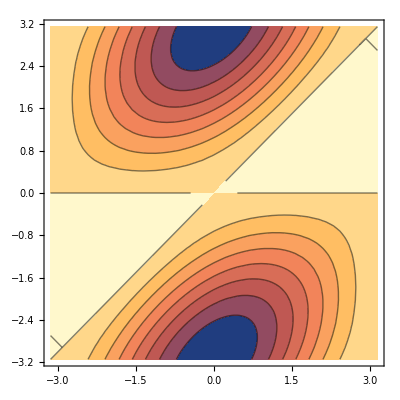

```mathematica
ContourPlot[w2 ,{ϕ1,-Pi,Pi},{ϕ2,-Pi,Pi}]
```

```mathematica
Plot3D[w1,{ϕ1,-Pi,Pi},{ϕ2,-Pi,Pi},PlotRange->All]
```

-Graphics3D-

Purity of the evolved state only with gravity

```mathematica
rho = (1/4)*{{1, Exp[-I phi1], Exp[-I phi2], 1}, {Exp[I phi1], 1, Exp[I (phi1-phi2)], Exp[I phi1]}, {Exp[I phi2], Exp[I (phi2-phi1)], 1, Exp[I phi2]}, {1, Exp[-I phi1], Exp[-I phi2], 1}};
MatrixForm[rho]
```

(1/4 | ⅇ^(-ⅈ phi1)/4 | ⅇ^(-ⅈ phi2)/4 | 1/4
ⅇ^(ⅈ phi1)/4 | 1/4 | 1/4 ⅇ^(ⅈ (phi1-phi2)) | ⅇ^(ⅈ phi1)/4
ⅇ^(ⅈ phi2)/4 | 1/4 ⅇ^(ⅈ (-phi1+phi2)) | 1/4 | ⅇ^(ⅈ phi2)/4
1/4 | ⅇ^(-ⅈ phi1)/4 | ⅇ^(-ⅈ phi2)/4 | 1/4)

```mathematica
rhosqared = FullSimplify[rho.rho]
```

{{1/4,ⅇ^(-ⅈ phi1)/4,ⅇ^(-ⅈ phi2)/4,1/4},{ⅇ^(ⅈ phi1)/4,1/4,1/4 ⅇ^(ⅈ (phi1-phi2)),ⅇ^(ⅈ phi1)/4},{ⅇ^(ⅈ phi2)/4,1/4 ⅇ^(-ⅈ (phi1-phi2)),1/4,ⅇ^(ⅈ phi2)/4},{1/4,ⅇ^(-ⅈ phi1)/4,ⅇ^(-ⅈ phi2)/4,1/4}}

```mathematica
FullSimplify[Tr[rhosqared]]
```

1

Purity of the evolved state after gravity

```mathematica
$Assumptions=phi12∈Reals &&phi13∈Reals && phi14∈Reals && phi23∈Reals&& phi24∈Reals&& phi34∈Reals && A12∈PositiveReals &&A13∈PositiveReals && A14∈PositiveReals && A23∈PositiveReals && A24∈PositiveReals && A34∈PositiveReals && B12∈PositiveReals &&B13∈PositiveReals && B14∈PositiveReals && B23∈PositiveReals && B24∈PositiveReals && B34∈PositiveReals;
rho12 = Exp[I phi12]Exp[-A12^2]Exp[-B12^2];
rho13 = Exp[I phi13]Exp[-A13^2]Exp[-B13^2];
rho14 = Exp[I phi14]Exp[-A14^2]Exp[-B14^2];
rho23 = Exp[I phi23]Exp[-A23^2]Exp[-B23^2];
rho24 = Exp[I phi24]Exp[-A24^2]Exp[-B24^2];
rho34 = Exp[I phi34]Exp[-A34^2]Exp[-B34^2];
rho = FullSimplify[(1/4)*{{ 1, Conjugate[rho12] , rho13, rho23}, {rho12, 1, rho14, rho24}, {Conjugate[rho13], Conjugate[rho14], 1, Conjugate[rho34]}, {Conjugate[rho23], Conjugate[rho24], rho34, 1}}];
MatrixForm[rho]
```

(1/4 | 1/4 ⅇ^(-A12^2-B12^2-ⅈ phi12) | 1/4 ⅇ^(-A13^2-B13^2+ⅈ phi13) | 1/4 ⅇ^(-A23^2-B23^2+ⅈ phi23)
1/4 ⅇ^(-A12^2-B12^2+ⅈ phi12) | 1/4 | 1/4 ⅇ^(-A14^2-B14^2+ⅈ phi14) | 1/4 ⅇ^(-A24^2-B24^2+ⅈ phi24)
1/4 ⅇ^(-A13^2-B13^2-ⅈ phi13) | 1/4 ⅇ^(-A14^2-B14^2-ⅈ phi14) | 1/4 | 1/4 ⅇ^(-A34^2-B34^2-ⅈ phi34)
1/4 ⅇ^(-A23^2-B23^2-ⅈ phi23) | 1/4 ⅇ^(-A24^2-B24^2-ⅈ phi24) | 1/4 ⅇ^(-A34^2-B34^2+ⅈ phi34) | 1/4)

```mathematica
rhosqared = rho.rho;
```

```mathematica
FullSimplify[Tr[rhosqared]]
```

1/8 (2+ⅇ^(-2 (A12^2+B12^2))+ⅇ^(-2 (A13^2+B13^2))+ⅇ^(-2 (A14^2+B14^2))+ⅇ^(-2 (A23^2+B23^2))+ⅇ^(-2 (A24^2+B24^2))+ⅇ^(-2 (A34^2+B34^2)))